## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
<<IGraphM`
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"BigSur 8.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"Additional Bioinformatics Functions.nb"}]];
```

IGraph/M 0.6.2 (July 25, 2022)
Evaluate IGDocumentation[] to get started.

ReplacePart::argrx: ReplacePart called with 2 arguments; 3 arguments are expected.

```mathematica
lowcRows[l_,min_]:=With[{x=Transpose[l]},Select[Range[Length[x]],Total[x[[#]]]>=min&]];
lowExRows[mat_, x_]:= Module[{means},
means = Mean/@mat;
Select[Range[Length[means]],means[[#]]>=x&]
];
```

## Load data

```mathematica
smallTest = Import["../testthat/fixtures/test_counts.mtx"];
```

```mathematica
smallTestGenes = Import["../testthat/fixtures/test_Genes.csv"][[2;;]];
```

```mathematica
smallTestCells = Import["../testthat/fixtures/test_Cells.csv"][[2;;]];
```

```mathematica
Dimensions[smallTest]
```

{254,250}

```mathematica
smallTestMatpac = {smallTest, smallTestGenes, smallTestCells};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
rajFull = Import["../testthat/fixtures/arjunrajrawcounts2.mtx"];
rajGenes = Import["../testthat/fixtures/arjunrajgenenames2.csv"];
rajCells = Import["../testthat/fixtures/arjunrajcellnames2.csv"];
```

```mathematica
kcells= lowcRows[rajFull,1300];
```

```mathematica
Length[kcells]
```

3117

```mathematica
kgenes = lowExRows[rajFull, 0.001];
```

```mathematica
Length[kgenes]
```

14695

```mathematica
Min[Total/@rajFull]
```

8

```mathematica
rajMatpac = {rajFull[[kgenes,kcells]], Flatten[rajGenes][[kgenes]], Flatten[rajCells][[kcells]]};
```

```mathematica
raj2k = {rajMatpac[[1]][[1;;2000]], rajMatpac[[2]][[1;;2000]],rajMatpac[[3]]};
```

```mathematica
Export["raj2k.mx",raj2k];
```

```mathematica
Dimensions/@rajMatpac
```

{{14695,3117},{14695},{3117}}

```mathematica
Export["../testthat/fixtures/rajSubs.mtx",rajMatpac[[1]]];
Export["../testthat/fixtures/rajSubGenes.csv",rajMatpac[[2]]];
Export["../testthat/fixtures/rajSubCells.csv", rajMatpac[[3]]];
```

## Residuals, eta/theta, and c’s

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

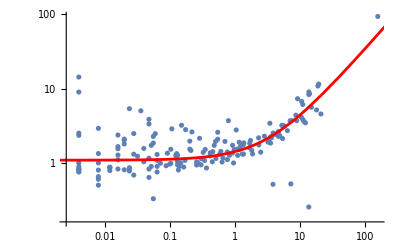

```mathematica
etaTheta=Values@TwoComponentCL1[smallTestMatpac, 250];
```

```mathematica
Export["etaTheta.txt", etaTheta]
```

etaTheta.txt

```mathematica
TwoComponentCL1All[matpac_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params,params2},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
newmat=mat;
newgenetotals=genetotals;
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x, NormFunction->(Total@Abs[#]&)];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ η + θ*μ)/.params, {μ, 10^-6, 10^6}, PlotStyle-> Red]]];
params]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

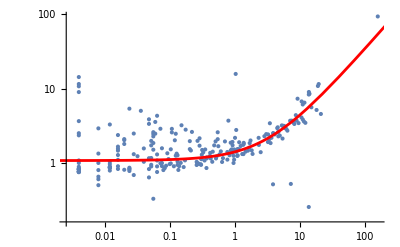

{0.0797936,0.331465}

```mathematica
etaTheta=Values@TwoComponentCL1All[smallTestMatpac]
```

```mathematica
Export["etaTheta.txt", etaTheta]
```

etaTheta.txt

```mathematica
TwoComponentCL1AllThetaOnly[matpac_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params,params2},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
newmat=mat;
newgenetotals=genetotals;
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
Print[Length[data]];
params=FindFit[Log[data], {Log[1+ θ*E^x],{ θ>0}},  {{θ,0.1}}, x, NormFunction->(Total@Abs[#]&)];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ θ*μ)/.params, {μ, 10^-6, 10^6}, PlotStyle-> Red]]];
params]
```

```mathematica
Options[TwoComponentCThetaOnly]={"Sample Goal"-> 3000, "zero eta"->True };
TwoComponentCThetaOnly[matpac_, OptionsPattern[]]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data,stop,indices,θlist,temp, params, t1},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[OptionValue["Sample Goal"]/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
indices=Partition[RandomSample[Range[Length[newgenetotals]]], UpTo[200]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues={};θlist={};data={};
For[k=1,k<= Length[indices],k++,
fittedjvalues=Join[fittedjvalues, Table[j/.FindRoot[Total@((newmat[[i]]/newematrix[[i]]-1)^2/(1/newematrix[[i]]+j )) +1-n, {j,1}, Method-> "Secant"], {i, indices[[k]]}]];
data=N[Select[Transpose[{newgenetotals[[Flatten[indices[[1;;k]]]]]/n, 1+fittedjvalues*newgenetotals[[Flatten[indices[[1;;k]]]]]/n}], Last[#]>0&]];
If[OptionValue["zero eta"],
params=Join[{η->0},FindFit[Log[data], {Log[1+ θ*E^x],θ>0},{{θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}]],
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}]];
AppendTo[θlist,{k,θ/.params}];
NotebookDelete[t1];NotebookDelete[stop];
t1=PrintTemporary[Last/@θlist];
NotebookDelete[temp];
temp=PrintTemporary[Grid[{{
ListPlot[θlist, Joined-> True, PlotRange-> {{1,Length[indices]},{0,Automatic}}],
Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]
}}]];
stop=PrintTemporary[Button["Stop Operation",Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]];
Print[{200k "genes tested", params}];FrontEndTokenExecute["EvaluatorAbort"]]];];
NotebookDelete[stop];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]];
{200k "genes tested", params}]
```

```mathematica
Options[TwoComponentCThetaOnlyVec]={"zero eta"->True,"Tolerance"->1.*^-12,"Max Iterations"->100};

TwoComponentCThetaOnlyVec[matpac_,OptionsPattern[]]:=Module[{mat,depthlist,n,genetotals,ematrix,a,b,lo,j,f,fp,jnew,bad,tol,maxit,k,data,params, keep, bin, counts, w},mat=matpac[[1]];
depthlist=Total/@N[Transpose[mat]]/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
ematrix=KroneckerProduct[genetotals,depthlist];
a=(mat/ematrix-1)^2;
b=1/ematrix;
lo=-(Min/@b);(*j must exceed this per gene*)tol=OptionValue["Tolerance"];
maxit=OptionValue["Max Iterations"];
j=ConstantArray[1.,Length[genetotals]];
Do[f=(Total/@(a/(b+j)))-(n-1);
fp=-(Total/@(a/(b+j)^2));
jnew=j-f/fp;
bad=UnitStep[lo-jnew];(*1 where the step leaves the domain*)jnew=(1-bad) jnew+bad (j+lo)/2;(*bisect toward the pole instead*)If[Max[Abs[jnew-j]]<tol,j=jnew;Break[]];
j=jnew,{k,maxit}];
data=Transpose[{genetotals/n,1+j*genetotals/n}];keep=Flatten@Position[Last/@data,_?Positive];data=N[data[[keep]]];bin=Floor[Log[genetotals[[keep]]]/0.5];counts=Counts[bin];w=1./Sqrt[Lookup[counts,bin]];               (*each half-log bin contributes equally*)

params=Join[{η->0},FindFit[Log[data],{Log[1+θ*E^x],θ>0},{{θ,0.1}},x,NormFunction->(Total[w*Abs[#]]&), MaxIterations->1000]];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+θ*μ)/. params,{μ,Min[First/@data],Max[First/@data]},PlotRange->All,PlotStyle->Red,Frame->True,FrameLabel->{"mean expression (μ)","1+η+θμ"}]]];
{Length[genetotals] "genes tested",params}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

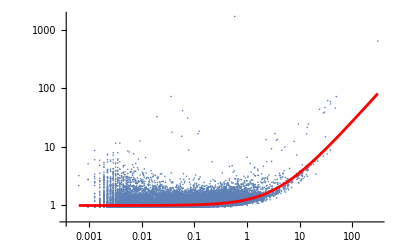

{14695 genes tested,{η→0,θ→0.261967}}

```mathematica
rajthetaOnly2=TwoComponentCThetaOnlyVec[rajMatpac]
```

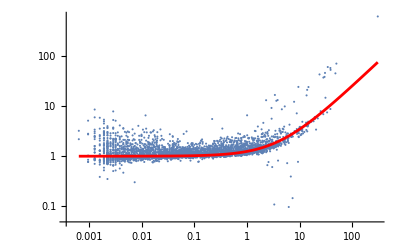

{η→0,θ→0.248263}

```mathematica
rajthetaOnly=TwoComponentCThetaOnly[rajMatpac, "Sample Goal"->5000][[2]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

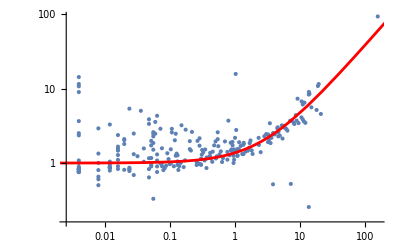

{0.369289}

```mathematica
thetaOnly=Values@TwoComponentCL1AllThetaOnly[smallTestMatpac]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

14683

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

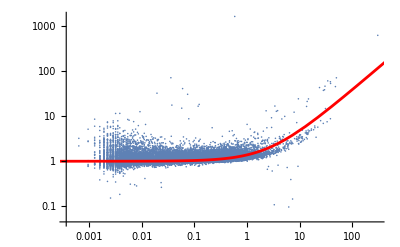

{0.382955}

```mathematica
rajTheta = Values@TwoComponentCL1AllThetaOnly[rajMatpac]
```

```mathematica
Export["thetaOnly.txt", thetaOnly]
```

thetaOnly.txt

```mathematica
Options[BigSurAlt7Test]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Find Communities"-> True};

BigSurAlt7Test[matpac_, η_, θ_,filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,clist, negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities,κ1,κ2,κ3,κ4},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
n=Width[mat];
m=Length[genetotals];
clist=√(η/#+ θ)&/@N[genetotals/n];
Print["Started on",CurrentDate[]];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
Share[];
ematrix = KroneckerProduct[genetotals, depthlist];
Share[];
pmatrix =(mat-ematrix)/(√(ematrix(1+clist^2 ematrix)))  ;
Export["residuals.csv", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Share[];
Export["mcfanos.csv", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κ1=FanoCum1[ematrix,clist,n];Share[];
	κ2=FanoCum2[ematrix,clist,n];Share[];
	κ3=FanoCum3[ematrix,clist,n];Share[];
	κ4=FanoCum4[ematrix,clist,n];Share[];
	κlists={κ1,κ2,κ3,κ4};
(*κlists=FanoCumulants5CFAlt[ematrix,clist,n];*);
Export["FK1.csv",κ1];
Export["FK2.csv",κ2];
Export["FK3.csv",κ3];
Export["FK4.csv",κ4];
Share[];
Print["Fano cumulants calculated"];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
Share[];
Print["Cornish-Fisher coefficients calculated"];
Export["FCF1.csv",polylist[[1]]];
Export["FCF2.csv",polylist[[2]]];
Export["FCF3.csv",polylist[[3]]];
Export["FCF4.csv",polylist[[4]]];
Export["FCF5.csv",polylist[[5]]];
Share[];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export["pccmatrix.csv", pccmatrix];
Print["Modified corrected correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentListsAltNew[genetotals,depthlist, η, θ, n];
Export["invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
Share[];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCFAlt[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],clist,n];
Export["CK1.csv", ccmats[[1]]];
Export["CK2.csv", ccmats[[2]]];
Export["CK3.csv", ccmats[[3]]];
Export["CK4.csv", ccmats[[4]]];
]
```

```mathematica
Directory[]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
thetaOnly[[1]]
```

0.369289

```mathematica
SetDirectory[".."]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests

```mathematica
SetDirectory["RajThetaOnly"];
```

```mathematica
rajTheta[[1]]
```

0.382955

```mathematica
BigSurAlt7Test[rajMatpac,η/.rajthetaOnly2[[2]],θ/.rajthetaOnly2[[2]],"x", "Correlations"->True ]
```

Started onMon 28 Sep 2026 10:43:04GMT-7

Folder name is

foldername$61240

Modified, corrected Fano factors acquired and saved10:44:54GMT-7TimeObject[{10,44,54.215525},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 10:54:21GMT-7TimeObject[{10,54,21.627435},Instant,-7.]

inverse squareroot Fano moments acquired and saved 10:57:05GMT-7TimeObject[{10,57,5.820942},Instant,-7.]

```mathematica
SetDirectory["OneComponent"];
BigSurAlt7Test[smallTestMatpac, 0., thetaOnly[[1]],"x", "Correlations"->True ]
```

Started onFri 25 Sep 2026 16:20:55GMT-7

Folder name is

foldername$48786

Modified, corrected Fano factors acquired and saved16:20:56GMT-7TimeObject[{16,20,56.327578},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 16:20:58GMT-7TimeObject[{16,20,58.88966},Instant,-7.]

inverse squareroot Fano moments acquired and saved 16:25:13GMT-7TimeObject[{16,25,13.41612},Instant,-7.]

```mathematica
SetDirectory[".."];
(*CreateDirectory["TwoComponent"];*)
SetDirectory["TwoComponent"]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/TwoComponent

```mathematica
BigSurAlt7Test[smallTestMatpac, etaTheta[[1]], etaTheta[[2]],"x", "Correlations"->True ]
```

Started onFri 25 Sep 2026 15:59:42GMT-7

Folder name is

foldername$38926

Modified, corrected Fano factors acquired and saved15:59:43GMT-7TimeObject[{15,59,43.745868},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 15:59:46GMT-7TimeObject[{15,59,46.308736},Instant,-7.]

inverse squareroot Fano moments acquired and saved 16:04:04GMT-7TimeObject[{16,4,4.054545},Instant,-7.]

```mathematica
Export["test_Genes.csv",smallTestMatpac[[2]]]
```

test_Genes.csv

```mathematica
Context[FanoCum1]
```

Global`

```mathematica
?FanoCum1
```

## Test that results are consistent between platforms

```mathematica
theta = 0.2536582;
```

```mathematica
Directory[]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
Dimensions/@raj2k
```

{{2000,3117},{2000},{3117}}

```mathematica
Export["raj2k."]
```

```mathematica
BigSurAlt7[raj2k, 0., theta,"RajTest",Automatic, "Correlations"->True ]
```

Started onTue 29 Sep 2026 11:20:01GMT-7

CreateDirectory::eexist: /Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/RajTest η=0. θ=0.254 already exists.

Folder name is

RajTest η=0. θ=0.254

Part::partw: Part 4 of … does not exist.

Modified, corrected Fano factors acquired and saved11:20:02GMT-7TimeObject[{11,20,2.546012},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Polynomials constructed.

Fano p-values acquired and saved11:20:05GMT-7TimeObject[{11,20,5.703867},Instant,-7.]

Modified corrected correlations acquired and saved 11:20:05GMT-7TimeObject[{11,20,5.829993},Instant,-7.]

inverse squareroot Fano moments acquired and saved 11:22:33GMT-7TimeObject[{11,22,33.680441},Instant,-7.]

Adjusted cumulants of the correlations acquired11:22:35GMT-7TimeObject[{11,22,35.702401},Instant,-7.]

Cornish Fisher Polynomial Coefficients acquired11:22:35GMT-7TimeObject[{11,22,35.922813},Instant,-7.]

1999000 equations gathered11:22:37GMT-7TimeObject[{11,22,37.31571},Instant,-7.]

Quick test complete.  Surviving parameter sets = 6703311:22:44GMT-7TimeObject[{11,22,44.090674},Instant,-7.]

TakeSmallestBy::tbnval: Values {31.1338,2.5025,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {41.2472,2.53462,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {37.0257,Abs[z],Abs[z],2.72888} produced by the function Abs cannot be used for numerical sorting because they are not all real.

General::stop: Further output of TakeSmallestBy::tbnval will be suppressed during this calculation.

True roots found11:22:49GMT-7TimeObject[{11,22,49.045724},Instant,-7.]

Quasiroots found 11:22:59GMT-7TimeObject[{11,22,59.17266},Instant,-7.]

x-values acquired11:22:59GMT-7TimeObject[{11,22,59.215712},Instant,-7.]

p-values acquired and saved11:22:59GMT-7TimeObject[{11,22,59.279864},Instant,-7.]

equivalent PCCs acquired and saved11:23:01GMT-7TimeObject[{11,23,1.802833},Instant,-7.]

For FDR = 0.02, the significance level is p < 6.20515×10^-4

significant PCCs identified and saved11:23:01GMT-7TimeObject[{11,23,1.837486},Instant,-7.]

ReplaceAll::reps: {GCAAGTCGATAT,GGACAATTTGTA,TGACAATTGACC,TAAGACTTCCCT,GAAACGGACAGA,TCGATTGGAGAA,AGGAAGATTTAA,GTCTCAAAGCAC,GTACGAACATAG,GGTCGAGATATA,«3107»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gene Network Object saved11:23:02GMT-7TimeObject[{11,23,2.06444},Instant,-7.]

Communities Identified11:23:02GMT-7TimeObject[{11,23,2.873555},Instant,-7.]

done

```mathematica
TakeSmallestBy[{31.133826348666645,2.502499482412763,Abs[z],Abs[z]},Abs,1]
```

TakeSmallestBy::tbnval: Values {31.1338,2.5025,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy[{31.1338,2.5025,Abs[z],Abs[z]},Abs,1]

```mathematica
TakeSmallestBy[(x/.{ToRules[NRoots[#,x]]}/._Complex-> z), Abs,1]
```

TakeSmallestBy[{31.1338,2.5025,Abs[z],Abs[z]},Abs,1]

```mathematica
res = Import["RajTest η=0. θ=0.254/RajTest_cell-specific residuals.mx"];
fanos = Import["RajTest η=0. θ=0.254/RajTest_modified_corrected_Fano factors.mx"];
fanops = Import["RajTest η=0. θ=0.254/RajTest_fanopvalues.mx"];

pccs = Import["RajTest η=0. θ=0.254/RajTest_pccmatrix.mx"];
logps = Import["RajTest η=0. θ=0.254/RajTest_logpvalues.mx"];
```

```mathematica
pccs
```

SparseArray[…]

```mathematica
Length[pccs["ExplicitValues"]]
Count[pccs["ExplicitValues"],_?Positive]
Count[pccs["ExplicitValues"],_?Negative]
```

61451

32850

28601

```mathematica
rCorrs = Import["rCorr.mtx"];
```

```mathematica
rCorrs = LowerTriangularize[rCorrs];
```

```mathematica
rCorrs
```

SparseArray[<67685>, {2000, 2000}]

```mathematica
Length[Intersection[rCorrs["ExplicitPositions"], pccs["ExplicitPositions"]]]
```

61097

```mathematica
rRes = Import["rRes.csv","Data"][[2;;,2;;]];
```

```mathematica
rRes==res
```

False

```mathematica
Dimensions[rRes]
```

{2000,3117}

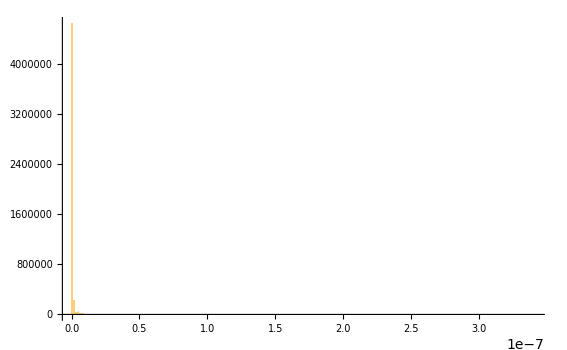

```mathematica
Histogram[Abs[Flatten[rRes-res]], PlotRange->All]
```

```mathematica
Max[Abs[Flatten[rRes-res]]]
```

3.41137×10^-7

```mathematica
rAll = Import["rAllPCC.csv","Data"][[2;;,2;;]];
```

```mathematica
Dimensions[rAll]
```

{2000,2000}

```mathematica
mcPCC=SparseArray[BoolEval[logps>-Log10[0.05]]*pccs];
```

```mathematica
mcPCC
```

SparseArray[<62925>, {2000, 2000}]

```mathematica
diffPCC=Abs[Extract[rAll,mcPCC["ExplicitPositions"]]-mcPCC["ExplicitValues"]];
```

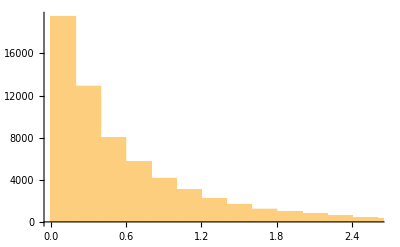

```mathematica
Histogram[diffPCC]
```

```mathematica
Max[diffPCC]
```

1.46596×10^-9

```mathematica
rmcFano = Import["rAllmcFanos.csv","Data"][[2;;,2;;]];
```

```mathematica
diffFano = Abs[Flatten[rmcFano]-Flatten[fanos]];
```

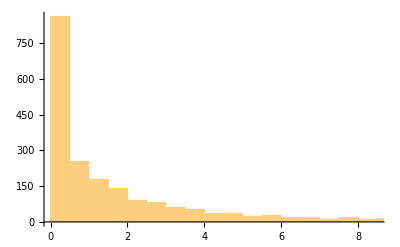

```mathematica
Histogram[diffFano]
```

```mathematica
Max[diffFano]
```

4.04306×10^-8

```mathematica
pccs[[18,11]]
```

-0.347658

```mathematica
mat=raj2k[[1]];
genetotals = Total/@mat;
n=Width[mat];
m=Length[genetotals];
clist=√(0/#+ theta)&/@N[genetotals/n];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
```

```mathematica
m1=InverseSqrtMomentListsAltNew[genetotals,depthlist,0.,theta,n];
m2=InverseSqrtMomentListsAltNew[genetotals,depthlist,0.,theta,n];
Max[Abs[Flatten[m1]/Flatten[m2]-1]]
```

0.458827

```mathematica
Max[Abs[m1[[All,All,2]]/m2[[All,All,2]]-1]]
```

0.458827

```mathematica
Quantile[Flatten[Abs[m1[[All,All,2]]/m2[[All,All,2]]-1]],{0.5,0.9,1.}]
```

{0.0104393,0.261873,0.458827}

```mathematica
test = Import["raj2k.mx"];
```

```mathematica
test==raj2k
```

True

```mathematica
BigSurAlt7[raj2k,0.,theta,"RajTest2",Automatic,"Correlations"->True]
```

Started onTue 29 Sep 2026 12:19:17GMT-7

CreateDirectory::eexist: /Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/RajTest2 η=0. θ=0.254 already exists.

Folder name is

RajTest2 η=0. θ=0.254

Part::partw: Part 4 of … does not exist.

Modified, corrected Fano factors acquired and saved12:19:18GMT-7TimeObject[{12,19,18.881823},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Polynomials constructed.

Fano p-values acquired and saved12:19:22GMT-7TimeObject[{12,19,22.035312},Instant,-7.]

Modified corrected correlations acquired and saved 12:19:22GMT-7TimeObject[{12,19,22.150058},Instant,-7.]

inverse squareroot Fano moments acquired and saved 12:21:49GMT-7TimeObject[{12,21,49.980378},Instant,-7.]

Adjusted cumulants of the correlations acquired12:21:51GMT-7TimeObject[{12,21,51.807549},Instant,-7.]

Cornish Fisher Polynomial Coefficients acquired12:21:51GMT-7TimeObject[{12,21,51.989861},Instant,-7.]

1999000 equations gathered12:21:53GMT-7TimeObject[{12,21,53.378076},Instant,-7.]

Quick test complete.  Surviving parameter sets = 6692912:22:00GMT-7TimeObject[{12,22,0.045893},Instant,-7.]

TakeSmallestBy::tbnval: Values {31.0732,2.50353,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {41.2349,2.53836,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {36.9994,Abs[z],Abs[z],2.73112} produced by the function Abs cannot be used for numerical sorting because they are not all real.

General::stop: Further output of TakeSmallestBy::tbnval will be suppressed during this calculation.

True roots found12:22:05GMT-7TimeObject[{12,22,5.23832},Instant,-7.]

Quasiroots found 12:22:15GMT-7TimeObject[{12,22,15.1825},Instant,-7.]

x-values acquired12:22:15GMT-7TimeObject[{12,22,15.22068},Instant,-7.]

p-values acquired and saved12:22:15GMT-7TimeObject[{12,22,15.28405},Instant,-7.]

equivalent PCCs acquired and saved12:22:17GMT-7TimeObject[{12,22,17.64646},Instant,-7.]

For FDR = 0.02, the significance level is p < 6.18591×10^-4

significant PCCs identified and saved12:22:17GMT-7TimeObject[{12,22,17.689493},Instant,-7.]

ReplaceAll::reps: {GCAAGTCGATAT,GGACAATTTGTA,TGACAATTGACC,TAAGACTTCCCT,GAAACGGACAGA,TCGATTGGAGAA,AGGAAGATTTAA,GTCTCAAAGCAC,GTACGAACATAG,GGTCGAGATATA,«3107»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gene Network Object saved12:22:17GMT-7TimeObject[{12,22,17.916724},Instant,-7.]

Communities Identified12:22:18GMT-7TimeObject[{12,22,18.704449},Instant,-7.]

done

```mathematica
theta
```

0.253658

```mathematica
raj2k = Import["raj2k.mx"];
```

```mathematica
Evaluate[{η->0.,θ->0.2536582}]
```

{η→0.,θ→0.253658}

```mathematica
noiserules={η->0.,θ->0.2536582};
```

```mathematica
Valuenoiserules
```

{η→0.,θ→0.253658}[η]

```mathematica
BigSur2[raj2k,{η->0.,θ->0.2536582},"RajTestNew","Correlations"->True]
```

Started onWed 30 Sep 2026 13:02:15GMT-7

Folder name is

RajTestNewWed 30 Sep 2026 13:02:15 η=0. θ=0.254

Part::partw: Part 4 of {SparseArray[<701720>, {2000, 3117}], <<1>>, {GCAAGTCGATAT, GGACAATTTGTA, TGACAATTGACC, <<12>>, <<3111>>, TAAAGCGTGTAC, ATTCTTGTGTAC}} does not exist.

Modified, corrected Fano factors acquired and saved13:02:15GMT-7TimeObject[{13,2,15.53552},Instant,-7.]

Fano p-values acquired and saved13:02:16GMT-7TimeObject[{13,2,16.9431},Instant,-7.]

Modified corrected correlations acquired and saved 13:02:17GMT-7TimeObject[{13,2,17.07633},Instant,-7.]

inverse squareroot Fano moments acquired and saved 13:02:30GMT-7TimeObject[{13,2,30.58129},Instant,-7.]

Adjusted cumulants of the correlations acquired13:02:31GMT-7TimeObject[{13,2,31.894395},Instant,-7.]

Cornish Fisher Polynomial Coefficients acquired13:02:32GMT-7TimeObject[{13,2,32.092353},Instant,-7.]

1999000 equations gathered13:02:33GMT-7TimeObject[{13,2,33.487707},Instant,-7.]

Quick test complete.  Surviving parameter sets = 6691113:02:37GMT-7TimeObject[{13,2,37.844356},Instant,-7.]

True roots found13:02:39GMT-7TimeObject[{13,2,39.760309},Instant,-7.]

Quasiroots found 13:02:39GMT-7TimeObject[{13,2,39.762934},Instant,-7.]

x-values acquired13:02:39GMT-7TimeObject[{13,2,39.786567},Instant,-7.]

p-values acquired and saved13:02:39GMT-7TimeObject[{13,2,39.850597},Instant,-7.]

equivalent PCCs acquired and saved13:02:40GMT-7TimeObject[{13,2,40.524875},Instant,-7.]

For FDR = 0.02, the significance level is p < 9.91813×10^-5

significant PCCs identified and saved13:02:40GMT-7TimeObject[{13,2,40.534346},Instant,-7.]

ReplaceAll::reps: {GCAAGTCGATAT,GGACAATTTGTA,TGACAATTGACC,TAAGACTTCCCT,GAAACGGACAGA,TCGATTGGAGAA,AGGAAGATTTAA,GTCTCAAAGCAC,GTACGAACATAG,GGTCGAGATATA,«3107»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gene Network Object saved13:02:40GMT-7TimeObject[{13,2,40.676197},Instant,-7.]

Communities Identified13:02:41GMT-7TimeObject[{13,2,41.028099},Instant,-7.]

done

```mathematica
inv=Import["RajTestNewWed 30 Sep 2026 11:10:58 η=0. θ=0.254/RajTestNew_invsqrtmoments.mx"];
```

```mathematica
invsqrtmoments2=InverseSqrtFanoMomentsListNB[genetotals,depthlist, 0., 0.2536582, n];
```

```mathematica
Table[(Last/@invsqrtmoments2[[i]])^(1/i),{i,4}]//TableForm
```

53.6718 | 2.52434 | 1.20636 | 1.07559 | 1.03585 | 1.00172 | 1.0002 | 1.00231
40.7229 | 4.66533 | 1.20667 | 1.07343 | 1.0343 | 1.00229 | 1.00044 | 1.00196
37.6272 | 7.46985 | 1.24041 | 1.08115 | 1.03727 | 1.00293 | 1.00066 | 1.00194
36.1975 | 9.7448 | 1.29033 | 1.09182 | 1.04145 | 1.00358 | 1.00086 | 1.002

```mathematica
Table[(Last/@invsqrtmoments[[i]])^(1/i),{i,4}]//TableForm
```

56.092 | 2.69137 | 1.20235 | 1.08247 | 1.03796 | 1.00548 | 1.00331 | 1.00204
41.6779 | 5.00132 | 1.20249 | 1.07965 | 1.03576 | 1.00514 | 1.00285 | 1.00173
38.217 | 7.85961 | 1.23388 | 1.08793 | 1.03849 | 1.00549 | 1.00286 | 1.00172
36.6226 | 10.1269 | 1.27816 | 1.09983 | 1.04255 | 1.00601 | 1.00298 | 1.00178

```mathematica
Table[(Last/@inv[[i]])^(1/i),{i,4}]//TableForm
```

56.5462 | 2.26757 | 1.22935 | 1.08126 | 1.03607 | 1.00361 | 1.00313 | 1.002
41.8272 | 3.95308 | 1.38173 | 1.07795 | 1.0342 | 1.00373 | 1.00261 | 1.00171
38.3055 | 6.54772 | 2.08147 | 1.08538 | 1.03695 | 1.00424 | 1.00256 | 1.0017
36.6858 | 8.80827 | 3.24482 | 1.09597 | 1.04096 | 1.00484 | 1.00262 | 1.00177

```mathematica
genetotals = Total/@raj2k[[1]];
```

```mathematica
pcc = Import["RajTestNewWed 30 Sep 2026 11:10:58 η=0. θ=0.254/RajTestNew_pccmatrix.mx"];
```

```mathematica
fanocorrectionmatrices=SqrtCorrectionmats[inv,genetotals];
```

```mathematica
mat = raj2k[[1]];
```

```mathematica
depthlist= (Total/@N[Transpose[mat]])/Total[Flatten[mat]];
ematrix = KroneckerProduct[genetotals, depthlist];
```

```mathematica
n=Width[mat];
```

```mathematica
ematrix[[1;;10,1;;10]]//TableForm
```

0.00232279 | 0.00380937 | 0.00314041 | 0.0109636 | 0.0040881 | 0.00215555 | 0.00235995 | 0.0251233 | 0.00250861 | 0.00886375
0.0104956 | 0.0172127 | 0.01419 | 0.049539 | 0.0184722 | 0.00973988 | 0.0106635 | 0.11352 | 0.0113352 | 0.040051
0.044305 | 0.0726602 | 0.0599004 | 0.20912 | 0.0779768 | 0.041115 | 0.0450139 | 0.479203 | 0.0478494 | 0.169068
0.000688233 | 0.0011287 | 0.000930491 | 0.00324846 | 0.00121129 | 0.00063868 | 0.000699245 | 0.00744393 | 0.000743292 | 0.0026263
0.0314006 | 0.051497 | 0.0424537 | 0.148211 | 0.0552651 | 0.0291398 | 0.031903 | 0.339629 | 0.0339127 | 0.119825
0.0321749 | 0.0527668 | 0.0435005 | 0.151866 | 0.0566278 | 0.0298583 | 0.0326897 | 0.348004 | 0.0347489 | 0.122779
0.00748454 | 0.0122746 | 0.0101191 | 0.035327 | 0.0131728 | 0.00694565 | 0.00760429 | 0.0809527 | 0.0080833 | 0.028561
0.0129904 | 0.0213043 | 0.017563 | 0.0613147 | 0.0228631 | 0.0120551 | 0.0131982 | 0.140504 | 0.0140296 | 0.0495714
0.0309705 | 0.0507916 | 0.0418721 | 0.146181 | 0.0545081 | 0.0287406 | 0.031466 | 0.334977 | 0.0334481 | 0.118183
0.0638336 | 0.104687 | 0.0863031 | 0.301295 | 0.112347 | 0.0592376 | 0.064855 | 0.690424 | 0.0689403 | 0.243589

```mathematica
clist = √0.2536582&/@N[genetotals/n];
```

```mathematica
ccmats=CorrelationCumulantsNB[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],clist,n];
```

```mathematica
ccmats[[4,1;;10,1;;10]]*10^9//TableForm
```

2395.05 | 136.046 | 19.5918 | 1.2036×10^7 | 30.0565 | 29.1334 | 223.509 | 100.054 | 30.5938 | 13.1342
136.046 | 7.73968 | 1.11975 | 683425. | 1.7153 | 1.66279 | 12.7084 | 5.69461 | 1.74587 | 0.752064
19.5918 | 1.11975 | 0.164238 | 98311. | 0.25049 | 0.24289 | 1.83555 | 0.824957 | 0.254913 | 0.110906
1.2036×10^7 | 683425. | 98311. | 6.04903×10^10 | 150876. | 146239. | 1.12295×10^6 | 502569. | 153575. | 65878.1
30.0565 | 1.7153 | 0.25049 | 150876. | 0.382572 | 0.370932 | 2.8133 | 1.26319 | 0.389348 | 0.16886
29.1334 | 1.66279 | 0.24289 | 146239. | 0.370932 | 0.359647 | 2.72707 | 1.22455 | 0.3775 | 0.163755
223.509 | 12.7084 | 1.83555 | 1.12295×10^6 | 2.8133 | 2.72707 | 20.8711 | 9.34896 | 2.8635 | 1.232
100.054 | 5.69461 | 0.824957 | 502569. | 1.26319 | 1.22455 | 9.34896 | 4.19044 | 1.28568 | 0.554357
30.5938 | 1.74587 | 0.254913 | 153575. | 0.389348 | 0.3775 | 2.8635 | 1.28568 | 0.396244 | 0.17183
13.1342 | 0.752064 | 0.110906 | 65878.1 | 0.16886 | 0.163755 | 1.232 | 0.554357 | 0.17183 | 0.0750514

```mathematica
pccmatrix = pcc;
```

```mathematica
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
```

```mathematica
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pcc];
augmentedParameters=Transpose[SymmetricMatrixToListNew/@Append[polymatrix, pccSignmatrix]];
```

```mathematica
Length[augmentedParameters]
```

1999000

```mathematica
augmentedParameters[[1;;10]]//TableForm
```

-0.0314487 | 0.0109475 | 0.000233332 | 0.00178023 | 0.00059734 | 1
0.00156145 | 0.0162951 | 0.00205638 | 0.000614149 | 0.000139344 | -1
-0.00203052 | 0.0178013 | 0.00147255 | 0.0000832986 | 1.54866×10^-6 | 1
485.464 | -8.96341 | -893.882 | 2.80728 | 136.136 | 1
28.9941 | -1.50373 | -52.2179 | 0.472833 | 7.74424 | -1
4.57592 | -0.397144 | -8.38633 | 0.131775 | 1.26851 | 1
0.0230088 | 0.015647 | 0.00214242 | 0.0007599 | 0.00018805 | -1
0.0048407 | 0.0177489 | 0.00174018 | 0.0000994174 | 1.22971×10^-6 | -1
0.00940028 | 0.0178799 | 0.000859619 | 0.0000350229 | 1.27472×10^-6 | -1
6.85128 | -0.536117 | -12.4762 | 0.174609 | 1.87588 | -1

```mathematica
xlist=ImprovedFindXAlt[augmentedParameters, 2, genetotals, 0.02];
```

Quick test complete.  Surviving parameter sets = 6237311:27:47GMT-7TimeObject[{11,27,47.780698},Instant,-7.]

TakeSmallestBy::tbnval: Values {24.6931,2.50364,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {34.3094,2.53245,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {30.8491,2.73037,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

General::stop: Further output of TakeSmallestBy::tbnval will be suppressed during this calculation.

True roots found11:27:51GMT-7TimeObject[{11,27,51.870859},Instant,-7.]

Quasiroots found 11:28:00GMT-7TimeObject[{11,28,0.828497},Instant,-7.]

```mathematica
table=Table[{1, x,x^2,x^3, x^4,0}, {x,{-k,- (2k)/3, -k/3, 0, k/3, (2k)/3,k}}]/.k-> √2 InverseErfc[2. 10^-2];
```

```mathematica
√2 InverseErfc[2. 10^-2]
```

2.32635

```mathematica
passedTest=Flatten[SparseArray[BoolEval[QuickTest6CFAltNew[augmentedParameters, table]==7]]["ExplicitPositions"]];
```

```mathematica
Export["passedTestK.mx",passedTest];
```

```mathematica
Directory[]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
QuickTest6CFAltNew=
Compile[{{paramslist, _Real, 2}, {table, _Real,2}},
Abs[Total[#]]&/@Outer[Sign[Dot[#1,#2]]&,paramslist,table ,1],RuntimeAttributes->{Listable}, Parallelization->True]
```

```mathematica
trueroots =  Flatten[TakeSmallestBy[(x/.{ToRules[NRoots[#,x]]}/._Complex-> z), Abs,1]&/@(#.{1, x, x^2, x^3, x^4,0}==0&/@survivingparams)];
Print["True roots found",TimeObject[Now]];
```

```mathematica
NRoots[poly[[644]],x]
```

x==-2.90789-0.358355 ⅈ||x==-2.90789+0.358355 ⅈ||x==2.08093-2.76968 ⅈ||x==2.08093+2.76968 ⅈ

```mathematica
TakeSmallestBy[(NRoots[poly[[644]],x]/.z_?_Complex->Nothing),Abs,1]
```

TakeSmallestBy::invrp: The argument x==-2.90789-0.358355 ⅈ||x==-2.90789+0.358355 ⅈ||x==2.08093-2.76968 ⅈ||x==2.08093+2.76968 ⅈ is not a valid Association or a list.

TakeSmallestBy[x==-2.90789-0.358355 ⅈ||x==-2.90789+0.358355 ⅈ||x==2.08093-2.76968 ⅈ||x==2.08093+2.76968 ⅈ,Abs,1]

```mathematica
trueroots =  Flatten[TakeSmallestBy[(x/.{ToRules[NRoots[#,x]]}/.z_?_Complex->Nothing), Abs,1]&/@(#.{1, x, x^2, x^3, x^4,0}==0&/@pass)];
```

```mathematica
Length[trueroots]
```

62373

```mathematica
trueroots[[1;;10]]
```

{-2.50364,-2.53245,2.73037,-2.43731,-3.27812,-3.46605,2.8143,3.63885,2.57466,-3.32508}

```mathematica
pass=augmentedParameters[[passedTest]];
```

```mathematica
poly = #.{1, x, x^2, x^3, x^4,0}==0&/@pass;
```

```mathematica
x=.
```

```mathematica
roots1=((x/.{ToRules[NRoots[#,x]]}/._Complex-> z)&/@poly)/.{z->Nothing};
```

```mathematica
minRoot=TakeSmallestBy[#,Abs,1]&/@roots1[[1;;10]];
```

TakeSmallestBy::tbnval: Values {24.6931,2.50364,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {34.3094,2.53245,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {30.8491,2.73037,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

General::stop: Further output of TakeSmallestBy::tbnval will be suppressed during this calculation.

```mathematica
minRoot
```

{TakeSmallestBy[{-24.6931,-2.50364,z,z},Abs,1],TakeSmallestBy[{-34.3094,-2.53245,z,z},Abs,1],TakeSmallestBy[{-30.8491,2.73037,z,z},Abs,1],TakeSmallestBy[{-21.581,z,z,-2.43731},Abs,1],TakeSmallestBy[{-22.1282,z,z,-3.27812},Abs,1],TakeSmallestBy[{-25.7096,-3.46605,z,z},Abs,1],TakeSmallestBy[{-41.596,z,z,2.8143},Abs,1],TakeSmallestBy[{-26.8772,z,z,3.63885},Abs,1],TakeSmallestBy[{-27.666,z,z,2.57466},Abs,1],TakeSmallestBy[{-25.1367,-3.32508,z,z},Abs,1]}

```mathematica
TakeSmallestBy[{-24.69312669401002,-2.5036357585059035,z,z}/.z->Nothing,Abs,1]
```

{-2.50364}

```mathematica
?TakeSmallestBy
```

```mathematica
trueroots=(Module[{r=x/. {ToRules[NRoots[#.{1,x,x^2,x^3,x^4,0}==0,x]]}},r=Select[r,Element[#,Reals]||Abs[Im[#]]<10^-5&];
If[r==={},z,First[TakeSmallestBy[Re[r],Abs,1]]]]&)/@augmentedParameters;
```

$Aborted

```mathematica
roots1[[1;;50]]//TableForm
```

-24.6931 | -2.50364 | z | z
-34.3094 | -2.53245 | z | z
-30.8491 | 2.73037 | z | z
-21.581 | z | z | -2.43731
-22.1282 | z | z | -3.27812
-25.7096 | -3.46605 | z | z
-41.596 | z | z | 2.8143
-26.8772 | z | z | 3.63885
-27.666 | z | z | 2.57466
-25.1367 | -3.32508 | z | z
-30.653 | -2.94366 | z | z
-29.7619 | z | z | 2.55992
-31.4044 | -3.08696 | z | z
-27.5456 | z | z | 2.53336
-401.84 | z | z | 2.72908
-32.8963 | z | z | 3.6117
-2.71118 | z | z | 2.38173
-446.241 | z | z | 2.37302
z | z | -2.412 | 205.071
-64.6312 | z | z | 2.45758
-26.7628 | z | z | 3.3889
z | z | -2.3334 | 48.5392
-26.4213 | z | z | 2.93823
-35.0591 | z | z | 3.23676
-25.2515 | z | z | 2.54612
-30.6654 | z | z | 3.12197
-26.0179 | -2.37831 | z | z
-153.566 | z | z | 2.49495
-23.221 | -3.08351 | z | z
-2.36666 | z | z | 12.5413
-2.39559 | z | z | 16.2694
z | z | 2.92762 | 727.678
-22.0729 | -3.10329 | z | z
z | z | 2.62555 | 136.618
-57.6147 | z | z | 2.35436
-190.081 | z | z | 2.69474
-25.0494 | z | z | -2.51448
-68.1481 | z | z | 2.82164
z | z | 2.75507 | 24.165
-30.0934 | z | z | 2.91591
-28.1805 | z | z | 3.47386
-28.0017 | z | z | 3.61928
z | z | 3.51085 | 22.9245
z | z | 2.3731 | 42.1501
-6.51338 | z | z | 2.59753
-29.1351 | -2.51838 | z | z
-31.9411 | -3.35961 | z | z
-29.9981 | -3.16915 | z | z
-28.8487 | -3.54093 | z | z
-25.2185 | z | z | 2.66241

```mathematica
poly[[1;;10]]
```

{0.0410848+0.0179037 x+0.000654274 x^2+0.0000256448 x^3+1.04411×10^-6 x^4==0,0.0438057+0.0179432 x+0.000277055 x^2+9.94342×10^-6 x^3+4.67123×10^-7 x^4==0,-0.0525335+0.0179213 x+0.000434566 x^2+0.0000158067 x^3+7.24195×10^-7 x^4==0,0.0377953+0.0178827 x+0.00108031 x^2+0.0000468595 x^3+1.45671×10^-6 x^4==0,0.0466427+0.0178653 x+0.00128846 x^2+0.0000595845 x^3+1.51562×10^-6 x^4==0,0.0554177+0.017938 x+0.000647398 x^2+0.0000281491 x^3+1.04416×10^-6 x^4==0,-0.0645218+0.0177901 x+0.00156861 x^2+0.0000870309 x^3+1.45443×10^-6 x^4==0,-0.0759087+0.0178712 x+0.00070792 x^2+0.0000272229 x^3+1.09881×10^-6 x^4==0,-0.050455+0.0178931 x+0.00059749 x^2+0.0000224599 x^3+9.62306×10^-7 x^4==0,0.0537631+0.0178959 x+0.000581603 x^2+0.0000218429 x^3+9.40587×10^-7 x^4==0}

```mathematica
Export["testaugmentedParameters.mx",augmentedParameters]
```

testaugmentedParameters.mx

```mathematica
oparams = Import["/Users/bigcomputer/Downloads/testaugmentedParametersADL.mx"];
```

```mathematica
testO=QuickTest6CFAltNew[oparams, table];
```

```mathematica
Length[testO]
```

1999000

```mathematica
Dimensions[augmentedParameters]
```

{1999000,6}

```mathematica
paramdiff=Table[Flatten[Abs[oparams[[All,i]]]-Flatten[testO[[All,i]]]],{i,6}];
```

Part::partd1: Depth of object {3,1,1,1,1,3,5,1,1,1,«1998990»} is not sufficient for the given part specification.

Part::partd: Part specification {3, 1, 1, 1, 1, 3, 5, 1, 1, 1, 3, 3, 1, 3, 1, 3, 5, 1, 1, 1, 3, 1, 1, 1, 1, <<1998963>>, 1, 1, 1, 3, 7, 1, 1, 1, 1, 7, 1, 3}[[All,1]] is longer than depth of object.

Part::partd1: Depth of object {3,1,1,1,1,3,5,1,1,1,«1998990»} is not sufficient for the given part specification.

Part::partd: Part specification {3, 1, 1, 1, 1, 3, 5, 1, 1, 1, 3, 3, 1, 3, 1, 3, 5, 1, 1, 1, 3, 1, 1, 1, 1, <<1998963>>, 1, 1, 1, 3, 7, 1, 1, 1, 1, 7, 1, 3}[[All,2]] is longer than depth of object.

Part::partd1: Depth of object {3,1,1,1,1,3,5,1,1,1,«1998990»} is not sufficient for the given part specification.

General::stop: Further output of Part::partd1 will be suppressed during this calculation.

Part::partd: Part specification {3, 1, 1, 1, 1, 3, 5, 1, 1, 1, 3, 3, 1, 3, 1, 3, 5, 1, 1, 1, 3, 1, 1, 1, 1, <<1998963>>, 1, 1, 1, 3, 7, 1, 1, 1, 1, 7, 1, 3}[[All,3]] is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

```mathematica
passedTestO = Flatten[SparseArray[BoolEval[QuickTest6CFAltNew[oparams, table]==7]]["ExplicitPositions"]];
```

```mathematica
table//TableForm
```

1 | -2.32635 | 5.41189 | -12.5899 | 29.2886 | 0
1 | -1.5509 | 2.40529 | -3.73036 | 5.7854 | 0
1 | -0.775449 | 0.601322 | -0.466294 | 0.361588 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0.775449 | 0.601322 | 0.466294 | 0.361588 | 0
1 | 1.5509 | 2.40529 | 3.73036 | 5.7854 | 0
1 | 2.32635 | 5.41189 | 12.5899 | 29.2886 | 0

```mathematica
checkK = Outer[Sign[Dot[#1,#2]]&,augmentedParameters,table ,1];
checkA =  Outer[Sign[Dot[#1,#2]]&,oparams,table ,1];
```

```mathematica
(Abs[Total[#]]&/@checkK)[[1;;100]]
```

{5,1,1,3,3,3,5,1,1,3,3,3,1,3,1,3,5,1,3,1,3,1,1,1,3,1,5,1,5,1,1,3,3,3,5,3,1,1,1,3,1,3,1,5,1,3,3,5,3,3,1,3,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,1,3,3,3,1,5,1,3,1,3,3,1,1,1,5,1,1,1,1,1,1,1,3,1,1,3,1,3,3,3,1,1,1}

```mathematica
(Abs[Total[#]]&/@checkA)[[1;;100]]
```

{3,1,1,1,1,3,5,1,1,1,3,3,1,3,1,3,5,1,1,1,3,1,1,1,1,1,5,1,5,1,1,1,3,3,5,3,1,1,1,3,1,3,1,5,1,3,3,5,3,3,1,3,1,3,1,3,1,3,3,1,1,1,3,3,3,3,1,1,3,1,3,1,5,1,3,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,3,3,3,1,1,1}

```mathematica
Length[passedTestO]
```

67164

```mathematica
testTest=QuickTest6CFAltNew[augmentedParameters, table];
```

```mathematica
Length@testTest
```

1999000

```mathematica
Length[passedTest]
```

62373

```mathematica
k = Import["RajTestNewWed 30 Sep 2026 11:10:58 η=0. θ=0.254/"]
```

```mathematica
res2 = Import["RajTest2 η=0. θ=0.254/RajTest2_cell-specific residuals.mx"];
fanos2 = Import["RajTest2 η=0. θ=0.254/RajTest2_modified_corrected_Fano factors.mx"];
fanops2 = Import["RajTest2 η=0. θ=0.254/RajTest2_fanopvalues.mx"];

pccs2 = Import["RajTest2 η=0. θ=0.254/RajTest2_significantPCCs.mx"];
logps2 = Import["RajTest2 η=0. θ=0.254/RajTest2_logpvalues.mx"];
```

```mathematica
inv2 = Import["RajTest2 η=0. θ=0.254/RajTest2_invsqrtmoments.mx"];
inv = Import["RajTest η=0. θ=0.254/RajTest_invsqrtmoments.mx"];
```

```mathematica
inv==inv2
```

False

```mathematica
N[inv2]
```

{{{3.,54.444},{6.4052,3.06231},{13.6755,1.22092},{29.1982,1.08145},{62.34,1.03784},{510.263,1.00392},{4176.58,0.998794},{34186.,0.998755}},{{3.,1684.4},{6.4052,33.1497},{13.6755,1.50838},{29.1982,1.1629},{62.34,1.07253},{510.263,1.00806},{4176.58,0.998772},{34186.,0.99877}},{{3.,54120.2},{6.4052,666.044},{13.6755,2.09604},{29.1982,1.28128},{62.34,1.11935},{510.263,1.01369},{4176.58,0.999136},{34186.,0.999208}},{{3.,1.74413×10^6},{6.4052,14505.7},{13.6755,3.47399},{29.1982,1.44893},{62.34,1.18005},{510.263,1.02083},{4176.58,0.999886},{34186.,1.00007}}}

```mathematica
N[inv]
```

{{{3.,55.1753},{6.4052,2.45757},{13.6755,1.2256},{29.1982,1.07831},{62.34,1.03359},{510.263,1.00425},{4176.58,1.00122},{34186.,0.999178}},{{3.,1708.26},{6.4052,19.7675},{13.6755,1.51609},{29.1982,1.15557},{62.34,1.06553},{510.263,1.00846},{4176.58,1.00246},{34186.,0.999485}},{{3.,54891.2},{6.4052,371.032},{13.6755,2.1091},{29.1982,1.26687},{62.34,1.10904},{510.263,1.01407},{4176.58,1.00412},{34186.,1.00027}},{{3.,1.76901×10^6},{6.4052,8009.67},{13.6755,3.49343},{29.1982,1.42293},{62.34,1.1657},{510.263,1.02111},{4176.58,1.0062},{34186.,1.00153}}}

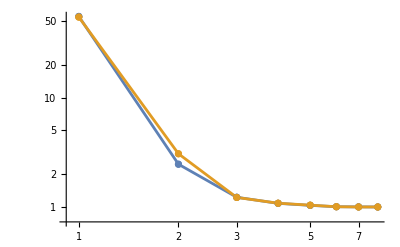

```mathematica
ListLogLogPlot[Evaluate[{Last/@inv[[1]], Last/@inv2[[1]]}], Joined-> True, Mesh-> Full]
```

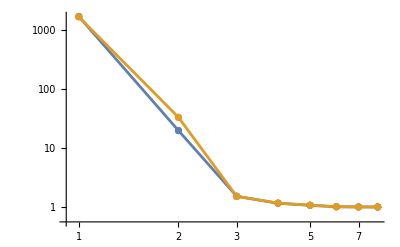

```mathematica
ListLogLogPlot[Evaluate[{Last/@inv[[2]], Last/@inv2[[2]]}], Joined-> True, Mesh-> Full]
```

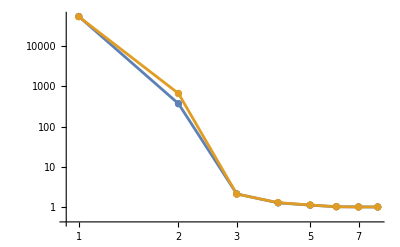

```mathematica
ListLogLogPlot[Evaluate[{Last/@inv[[3]], Last/@inv2[[3]]}], Joined-> True, Mesh-> Full]
```

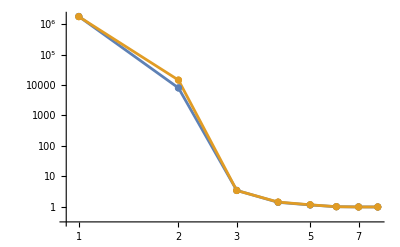

```mathematica
ListLogLogPlot[Evaluate[{Last/@inv[[4]], Last/@inv2[[4]]}], Joined-> True, Mesh-> Full]
```

```mathematica
pccs
```

SparseArray[…]

```mathematica
pccs2
```

SparseArray[…]

```mathematica
Complement[pccs["ExplicitPositions"],pccs2["ExplicitPositions"]]
```

Complement::heads: Heads List and {{1., 0.0294233, -0.00403586, 0.0110909, <<8>>53, <<1993>>, -0.00290426, -0.000773712}, <<1999>>} at positions 2 and 1 are expected to be the same.

```mathematica
Count[10^-(logps["ExplicitValues"]),0.]
Min[Select[10^-(logps["ExplicitValues"]),#>0&]]
```

13330

5.×10^-324

```mathematica
logpmatrix = logps;
```

```mathematica
lp=-Log[10]*logpmatrix["ExplicitValues"];   (*natural log p,negative*)
nn=Length[lp];o=Ordering[lp];
adj=lp[[o]]+Log[nn]-Log[Range[nn]];
adj=Reverse[FoldList[Min,Reverse[adj]]][[;;nn]];
Count[adj,x_/;x<Log[0.02]]
```

62925

```mathematica
Length[logpmatrix["ExplicitValues"]]
Quantile[logpmatrix["ExplicitValues"],{0,.25,.5,.75,1}]
```

67033

{0.301046,113.487,196.489,255.499,1.76226×10^10}

## Bug fix on ImprovedFindXAlt

```mathematica
raj2k=Import["raj2k.mx"];
```

```mathematica
theta = 0.2536582;
```

```mathematica
BigSurAlt7[raj2k,0.,theta,"RajTest3",Automatic,"Correlations"->True]
```

Started onTue 29 Sep 2026 13:38:33GMT-7

CreateDirectory::eexist: /Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/RajTest3 η=0. θ=0.254 already exists.

Folder name is

RajTest3 η=0. θ=0.254

Part::partw: Part 4 of {SparseArray[<701720>, {2000, 3117}], <<1>>, {GCAAGTCGATAT, GGACAATTTGTA, <<3114>>, ATTCTTGTGTAC}} does not exist.

Modified, corrected Fano factors acquired and saved13:38:34GMT-7TimeObject[{13,38,34.622676},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Polynomials constructed.

Fano p-values acquired and saved13:38:38GMT-7TimeObject[{13,38,38.001627},Instant,-7.]

Modified corrected correlations acquired and saved 13:38:38GMT-7TimeObject[{13,38,38.115802},Instant,-7.]

inverse squareroot Fano moments acquired and saved 13:41:03GMT-7TimeObject[{13,41,3.472323},Instant,-7.]

Adjusted cumulants of the correlations acquired13:41:05GMT-7TimeObject[{13,41,5.236928},Instant,-7.]

Cornish Fisher Polynomial Coefficients acquired13:41:05GMT-7TimeObject[{13,41,5.3862},Instant,-7.]

1999000 equations gathered13:41:06GMT-7TimeObject[{13,41,6.728484},Instant,-7.]

Quick test complete.  Surviving parameter sets = 6768213:41:13GMT-7TimeObject[{13,41,13.27115},Instant,-7.]

True roots found13:41:15GMT-7TimeObject[{13,41,15.50646},Instant,-7.]

Quasiroots found 13:41:15GMT-7TimeObject[{13,41,15.50883},Instant,-7.]

x-values acquired13:41:15GMT-7TimeObject[{13,41,15.52888},Instant,-7.]

p-values acquired and saved13:41:15GMT-7TimeObject[{13,41,15.59265},Instant,-7.]

equivalent PCCs acquired and saved13:41:17GMT-7TimeObject[{13,41,17.62914},Instant,-7.]

For FDR = 0.02, the significance level is p < -9.43419

significant PCCs identified and saved13:41:18GMT-7TimeObject[{13,41,18.59852},Instant,-7.]

ReplaceAll::reps: {GCAAGTCGATAT,GGACAATTTGTA,TGACAATTGACC,TAAGACTTCCCT,GAAACGGACAGA,TCGATTGGAGAA,AGGAAGATTTAA,GTCTCAAAGCAC,GTACGAACATAG,GGTCGAGATATA,«3107»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gene Network Object saved13:41:18GMT-7TimeObject[{13,41,18.757792},Instant,-7.]

Communities Identified13:41:18GMT-7TimeObject[{13,41,18.974786},Instant,-7.]

done

```mathematica
res3 = Import["RajTest3 η=0. θ=0.254/RajTest3_cell-specific residuals.mx"];
fanos3 = Import["RajTest3 η=0. θ=0.254/RajTest3_modified_corrected_Fano factors.mx"];
fanops3= Import["RajTest3 η=0. θ=0.254/RajTest3_fanopvalues.mx"];

pccs3 = Import["RajTest3 η=0. θ=0.254/RajTest3_pccmatrix.mx"];
logps3 = Import["RajTest3 η=0. θ=0.254/RajTest3_logpvalues.mx"];
```

```mathematica
pccs3
```

SparseArray[…]

```mathematica
rCorrsLT
```

SparseArray[…]

```mathematica
rCorrs = Import["rCorr2.mtx"];
```

```mathematica
rCorrsLT=LowerTriangularize[rCorrs];
```

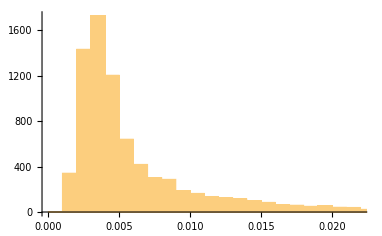

```mathematica
Histogram[Abs[rCorrsLT["ExplicitValues"]-Extract[pccs3,rCorrsLT["ExplicitPositions"]]]]
```

```mathematica
mcPCC=SparseArray[BoolEval[logps3>-Log10[0.02]]*pccs3];
```

```mathematica
Max[Abs[rCorrsLT["ExplicitValues"]-Extract[mcPCC,rCorrsLT["ExplicitPositions"]]]]
```

1.46596×10^-9

```mathematica
rPs
```

SparseArray[…]

```mathematica
logps3
```

SparseArray[<67682>, {2000, 2000}]

```mathematica
Max[Abs[rPs["ExplicitValues"]-Extract[logps3,rPs["ExplicitPositions"]]]]
```

213.146

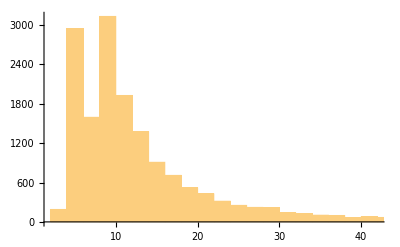

```mathematica
Histogram[Abs[rPs["ExplicitValues"]-Extract[logps3,rPs["ExplicitPositions"]]]]
```

```mathematica
Max[pccs3]
```

0.260956

```mathematica
rPs = Import["rPs2.mtx"];
```

```mathematica
Length[Intersection[rPs["ExplicitPositions"], logps3["ExplicitPositions"]]]
```

7982

```mathematica
Length[rPs["ExplicitPositions"]]/2
```

7982

```mathematica
Min[logps3["ExplicitValues"]]
```

0.0000889751

```mathematica
Length[logps3["ExplicitValues"]]
```

67682

```mathematica
m = Width[raj2k[[1]]];
```

```mathematica
sigcutofflist={#,#+Log[2],#+Log[3]}&@BHNewLog[-Log[10]*logps3["ExplicitValues"],0.02,Binomial[m,2]]
```

{-10.3757,-9.68253,-9.27707}

```mathematica
sigcutofflist[[1]]                          (*natural log cutoff*)
sigcutofflist[[1]]/Log[10]                  (*in-log10 units,negated*)
Length[logps3["ExplicitValues"]]
```

-10.3757

-4.5061

66907

## Test after fixing find X for older version of Mathematica

```mathematica
rCorr = Import["rNBCorr.mtx"];
rCorrPs = Import["rNBPs.mtx"];
```

```mathematica
rCorrNoRoot = Import["rRemoveRootSolve.mtx"];
rCorrPNoRoot=Import["rPsRemoveRootSolve.mtx"];
```

```mathematica
rCorrLowA = Import["rLowA.mtx"];
rCorrPLowA = Import["rPsLowA.mtx"]
```

SparseArray[…]

```mathematica
rCorrLowA=  LowerTriangularize[rCorrLowA];
```

```mathematica
rCorrPLowA =LowerTriangularize[rCorrPLowA];
```

```mathematica
rCorrNoRoot =  LowerTriangularize[rCorrNoRoot];
```

```mathematica
rCorr = LowerTriangularize[rCorr];
```

```mathematica
rCorrNoRoot
```

SparseArray[…]

```mathematica
mCorr =Import["RajTestNewWed 30 Sep 2026 13:02:15 η=0. θ=0.254/RajTestNew_pccmatrix.mx"];
mCorrPs = Import["RajTestNewWed 30 Sep 2026 13:02:15 η=0. θ=0.254/RajTestNew_logpvalues.mx"];
```

```mathematica
mGNO=  Import["RajTestNewWed 30 Sep 2026 13:02:15 η=0. θ=0.254/RajTestNew_gNOpccprime.mx"];
```

ReplaceAll::reps: {GCAAGTCGATAT,GGACAATTTGTA,TGACAATTGACC,TAAGACTTCCCT,GAAACGGACAGA,TCGATTGGAGAA,AGGAAGATTTAA,GTCTCAAAGCAC,GTACGAACATAG,GGTCGAGATATA,«3107»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
mGNO[[3]]
```

SparseArray[…]

```mathematica
m=Dimensions[raj2k[[1]]][[1]];
```

```mathematica
cut=BHNew[10^-(mCorrPs["ExplicitValues"]),0.02,Binomial[m,2] ];
```

```mathematica
mcPCC=SparseArray[BoolEval[mCorrPs>-Log10[cut]]*mCorr];
```

```mathematica
mcPCC
```

SparseArray[…]

```mathematica
rCorr
```

SparseArray[…]

```mathematica
Max[Abs[rCorr["ExplicitValues"]-Extract[mcPCC,rCorr["ExplicitPositions"]]]]
```

1.46596×10^-9

```mathematica
Max[Abs[rCorr["ExplicitValues"]-Extract[rCorrNoRoot,rCorr["ExplicitPositions"]]]]
```

0.

```mathematica
Max[Abs[rCorrNoRoot["ExplicitValues"]-Extract[rCorr,rCorrNoRoot["ExplicitPositions"]]]]
```

0.259517

```mathematica
Max[Abs[rCorrNoRoot["ExplicitValues"]-Extract[mcPCC,rCorrNoRoot["ExplicitPositions"]]]]
```

0.259517

```mathematica
Max[Abs[mcPCC["ExplicitValues"]-Extract[rCorrNoRoot,mcPCC["ExplicitPositions"]]]]
```

0.205033

```mathematica
Position[mcPCC["ExplicitValues"],0.20503315943084902]
```

{{9596}}

```mathematica
Max[Abs[rCorrLowA["ExplicitValues"]-Extract[rCorr,rCorrLowA["ExplicitPositions"]]]]
```

0.

```mathematica
Max[Abs[rCorrLowA["ExplicitValues"]-Extract[mcPCC,rCorrLowA["ExplicitPositions"]]]]
```

1.46596×10^-9

```mathematica
Max[rCorrPLowA["ExplicitValues"]]
```

-6.90833

```mathematica
Position[rCorrPLowA["ExplicitValues"],Max[rCorrPLowA["ExplicitValues"]]]
```

{{30},{3592}}

```mathematica
rCorrPLowA["ExplicitPositions"][[Flatten[Position[rCorrPLowA["ExplicitValues"],Max[rCorrPLowA["ExplicitValues"]]]]]]
```

{{548,522},{1904,1139}}

```mathematica
raj2k[[2]][[{548,522,1904,1139}]]
```

{AKAP11,AHNAK,CBX6,ATP5J}

```mathematica
Mean[raj2k[[1]][[#]]]&/@{548,522,1904,1139}//N
```

{0.356112,0.295797,0.2265,3.25281}

```mathematica
raj2k[[2]][[3592]]
```

Part::partw: Part 3592 of {A1BG,A1BG-AS1,A2M,A2M-AS1,AAAS,AACS,AADAT,AAED1,AAGAB,AAK1,«1990»} does not exist.

{A1BG,A1BG-AS1,A2M,A2M-AS1,AAAS,AACS,AADAT,AAED1,AAGAB,AAK1,AAMDC,AAMP,AAR2,AARD,AARS,AARS2,AARSD1,AASDH,AASDHPPT,AASS,AATF,AATK,ABAT,ABBA01017803.1,ABBA01031664.1,ABCA1,ABCA13,ABCA2,ABCA5,ABCA7,ABCB10,ABCB5,ABCB6,ABCB7,ABCB8,ABCB9,ABCC1,ABCC10,ABCC11,ABCC4,ABCC5,ABCD1,ABCD2,ABCD3,ABCD4,ABCE1,ABCF1,ABCF2,ABCF3,ABCG2,ABCG5,ABHD1,ABHD10,ABHD11,ABHD11-AS1,ABHD12,ABHD13,ABHD14A,ABHD14B,ABHD15,ABHD17A,ABHD17B,ABHD17C,ABHD2,ABHD3,ABHD4,ABHD5,ABHD6,ABHD8,ABI1,ABI2,ABL1,ABL2,ABLIM1,ABLIM3,ABR,ABRACL,ABT1,ABTB1,ABTB2,AC000068.5,AC000123.2,AC000123.3,AC002044.1,AC002116.7,AC002117.1,AC002310.12,AC002310.7,AC002454.1,AC002467.7,AC002550.5,AC002558.1,AC003075.4,AC003092.1,AC003665.1,AC003956.1,AC003986.7,AC004041.2,AC004069.2,AC004076.5,AC004158.2,AC004221.2,AC004381.6,AC004447.2,AC004540.5,AC004549.6,AC004623.2,AC004623.3,AC004854.4,AC004893.11,AC004951.6,AC004988.1,AC005019.3,AC005037.3,AC005076.5,AC005154.6,AC005224.2,AC005253.2,AC005253.4,AC005262.2,AC005281.1,AC005306.3,AC005329.7,AC005363.11,AC005480.1,AC005523.2,AC005540.3,AC005562.1,AC005592.2,AC005785.2,AC005785.5,AC005786.7,AC005932.1,AC005944.2,AC006077.3,AC006262.5,AC006369.2,AC006460.2,AC006486.10,AC006538.1,AC006547.14,AC006547.15,AC006547.8,AC006548.28,AC006942.4,AC006946.16,AC006946.17,AC006988.1,AC007038.7,AC007040.11,AC007131.2,AC007191.4,AC007193.9,AC007228.9,AC007246.3,AC007285.6,AC007383.3,AC007405.4,AC007566.10,AC007620.3,AC007773.2,AC007906.1,AC008074.1,AC008079.10,AC008440.5,AC008982.2,AC008991.1,AC009005.2,AC009065.4,AC009120.6,AC009133.12,AC009303.2,AC009403.2,AC009404.2,AC009495.2,AC009495.3,AC009495.4,AC009501.4,AC009505.2,AC009506.1,AC009784.3,AC009948.5,AC009961.3,AC010226.4,AC010883.5,AC010894.3,AC010976.2,AC010987.5,AC010987.6,AC011524.1,AC011558.5,AC012065.1,AC012123.1,AC012146.7,AC012309.5,AC012358.8,AC012360.4,AC012370.2,AC012487.2,AC013394.2,AC015971.2,AC016700.3,AC016700.5,AC016722.4,AC016738.4,AC016747.3,AC016831.7,AC016995.3,AC018462.2,AC018742.1,AC018816.3,AC018890.6,AC019100.3,AC019181.2,AC020571.3,AC021188.4,AC021451.1,AC022007.5,AC022154.7,AC023115.2,AC025171.1,AC025335.1,AC026202.3,AC027763.2,AC034220.3,AC062017.1,AC062029.1,AC064875.2,AC068039.4,AC068282.3,AC068499.10,AC068580.6,AC068831.10,AC072062.1,AC073043.1,AC073254.1,AC073333.8,AC073641.2,AC074117.10,AC074138.3,AC074183.4,AC074212.6,AC074286.1,AC074289.1,AC078941.1,AC079135.1,AC079305.10,AC079742.4,AC079807.2,AC079949.1,AC083826.1,AC083843.1,AC083843.4,AC083884.8,AC084219.4,AC084357.1,AC084809.2,AC084809.3,AC087884.1,AC090587.2,AC090673.1,AC091133.1,AC091729.9,AC092066.1,AC092168.2,AC092171.4,AC092301.3,AC092574.2,AC092670.1,AC092687.5,AC092835.2,AC093323.3,AC093388.3,AC093590.1,AC093673.5,AC093818.1,AC096559.1,AC096574.4,AC096772.6,AC097662.2,AC097721.2,AC097724.3,AC098591.1,AC098820.3,AC099850.1,AC104532.4,AC104653.1,AC104655.3,AC104667.3,AC105760.2,AC107081.5,AC108488.4,AC109351.1,AC110056.1,AC110615.1,AC113189.5,AC114271.2,AC114803.3,AC118344.1,AC127904.2,AC132825.1,AC133528.2,AC135048.13,AC137932.4,AC139100.4,AC142472.6,AC142528.1,AC144449.1,AC144652.1,AC145110.1,AC147651.4,AC156455.1,AC253572.1,ACAA1,ACAA2,ACACA,ACACB,ACAD10,ACAD11,ACAD8,ACAD9,ACADM,ACADS,ACADSB,ACADVL,ACAP1,ACAP2,ACAP2-IT1,ACAP3,ACAT1,ACAT2,ACBD3,ACBD4,ACBD5,ACBD7,ACCS,ACD,ACER3,ACIN1,ACLY,ACN9,ACO1,ACO2,ACOT11,ACOT13,ACOT2,ACOT7,ACOT8,ACOT9,ACOX1,ACOX3,ACP1,ACP2,ACP5,ACP6,ACRC,ACSBG1,ACSF2,ACSF3,ACSL1,ACSL3,ACSL4,ACSL6,ACSM3,ACSM5,ACSS1,ACSS2,ACTA1,ACTA2,ACTB,ACTBL2,ACTC1,ACTG1,ACTG2,ACTL10,ACTL6A,ACTN1,ACTN2,ACTN4,ACTR10,ACTR1A,ACTR1B,ACTR2,ACTR3,ACTR3B,ACTR5,ACTR6,ACTR8,ACTRT3,ACVR1,ACVR1B,ACVR1C,ACVR2A,ACVR2B,ACVR2B-AS1,ACY1,ACYP1,ACYP2,AD000684.2,AD001527.4,ADA,ADAL,ADAM10,ADAM11,ADAM15,ADAM17,ADAM19,ADAM22,ADAM23,ADAM9,ADAMTS1,ADAMTS12,ADAMTS13,ADAMTS16,ADAMTS17,ADAMTS3,ADAMTS9,ADAMTS9-AS2,ADAMTSL5,ADAR,ADARB1,ADAT1,ADAT2,ADAT3,ADCK1,ADCK2,ADCK3,ADCK4,ADCK5,ADCY1,ADCY2,ADCY3,ADCY6,ADCY7,ADCY9,ADD1,ADD3,ADH5,ADHFE1,ADI1,ADIPOR1,ADIPOR2,ADK,ADM,ADM5,ADNP,ADNP-AS1,ADNP2,ADO,ADORA2B,ADPGK,ADPRH,ADPRHL2,ADPRM,ADRBK1,ADRBK2,ADRM1,ADSL,ADSS,ADSSL1,ADTRP,AEBP1,AEBP2,AEN,AES,AF129408.17,AF131215.2,AF131215.3,AF131215.4,AF131215.9,AF196972.9,AF230666.2,AFAP1,AFAP1-AS1,AFAP1L1,AFAP1L2,AFF1,AFF3,AFF4,AFG3L2,AFMID,AFTPH,AGA,AGAP1,AGAP10,AGAP2,AGAP2-AS1,AGAP3,AGAP6,AGBL2,AGBL3,AGBL5,AGFG1,AGFG2,AGGF1,AGK,AGL,AGMO,AGO1,AGO2,AGO3,AGO4,AGPAT1,AGPAT2,AGPAT3,AGPAT4,AGPAT4-IT1,AGPAT5,AGPAT6,AGPAT9,AGPS,AGRN,AGT,AGTPBP1,AGTRAP,AHCTF1,AHCY,AHCYL1,AHCYL2,AHDC1,AHI1,AHNAK,AHNAK2,AHR,AHRR,AHSA1,AHSA2,AIDA,AIF1L,AIFM1,AIFM2,AIFM3,AIG1,AIM1,AIMP1,AIMP2,AIP,AJUBA,AK1,AK2,AK3,AK4,AK5,AK6,AK9,AKAP1,AKAP10,AKAP11,AKAP12,AKAP13,AKAP2,AKAP3,AKAP5,AKAP6,AKAP7,AKAP8,AKAP8L,AKAP9,AKIP1,AKIRIN1,AKIRIN2,AKNA,AKNAD1,AKR1A1,AKR1B1,AKR1E2,AKR7A2,AKT1,AKT1S1,AKT2,AKT3,AKTIP,AL022341.3,AL034553.1,AL049794.1,AL132988.1,AL133243.1,AL133243.2,AL133243.4,AL133493.2,AL136419.6,AL158801.1,AL161626.1,AL353147.1,AL359973.1,AL365181.2,AL589743.1,AL589822.1,AL845472.1,ALAD,ALAS1,ALCAM,ALDH16A1,ALDH18A1,ALDH1A1,ALDH1A3,ALDH1B1,ALDH1L1,ALDH1L2,ALDH3A2,ALDH3B1,ALDH4A1,ALDH5A1,ALDH6A1,ALDH7A1,ALDH9A1,ALDOA,ALDOC,ALG1,ALG10,ALG10B,ALG11,ALG12,ALG13,ALG14,ALG2,ALG3,ALG5,ALG6,ALG8,ALK,ALKBH1,ALKBH2,ALKBH3,ALKBH4,ALKBH5,ALKBH6,ALKBH7,ALKBH8,ALMS1,ALMS1-IT1,ALOX12,ALPK1,ALS2,ALS2CR11,ALS2CR12,ALX1,ALX3,ALYREF,AMACR,AMBRA1,AMD1,AMDHD1,AMDHD2,AMER1,AMFR,AMHR2,AMMECR1,AMMECR1L,AMN,AMN1,AMOT,AMOTL1,AMOTL2,AMPD2,AMPH,AMT,AMY2A,AMY2B,AMZ2,ANAPC1,ANAPC10,ANAPC11,ANAPC13,ANAPC15,ANAPC16,ANAPC2,ANAPC4,ANAPC5,ANAPC7,ANG,ANGEL1,ANGEL2,ANGPT1,ANGPT2,ANGPTL1,ANGPTL2,ANGPTL6,ANK2,ANK3,ANKAR,ANKDD1A,ANKEF1,ANKFY1,ANKH,ANKHD1,ANKHD1-EIF4EBP3,ANKIB1,ANKLE2,ANKMY1,ANKMY2,ANKRA2,ANKRD10,ANKRD10-IT1,ANKRD11,ANKRD12,ANKRD13A,ANKRD13B,ANKRD13C,ANKRD13D,ANKRD16,ANKRD17,ANKRD18B,ANKRD23,ANKRD26,ANKRD27,ANKRD28,ANKRD30B,ANKRD31,ANKRD32,ANKRD34A,ANKRD36,ANKRD36C,ANKRD37,ANKRD39,ANKRD40,ANKRD42,ANKRD44,ANKRD44-IT1,ANKRD45,ANKRD46,ANKRD49,ANKRD50,ANKRD52,ANKRD54,ANKRD6,ANKRD7,ANKRD9,ANKS1A,ANKS1B,ANKS3,ANKS6,ANKZF1,ANLN,ANO10,ANO4,ANO6,ANO7,ANO8,ANP32A,ANP32B,ANP32D,ANP32E,ANTXR1,ANTXR2,ANXA1,ANXA11,ANXA2,ANXA2R,ANXA4,ANXA5,ANXA6,ANXA7,ANXA9,AOC2,AP000240.9,AP000251.3,AP000304.12,AP000320.6,AP000437.3,AP000442.1,AP000487.5,AP000487.6,AP000577.2,AP000648.5,AP000662.4,AP000692.10,AP000692.9,AP000695.4,AP000695.6,AP000704.5,AP000866.2,AP000892.6,AP001062.7,AP001258.4,AP001347.6,AP001350.4,AP001372.2,AP001412.1,AP001429.1,AP001432.14,AP001462.6,AP001469.7,AP001469.9,AP001505.10,AP001615.9,AP002954.4,AP003068.23,AP003900.6,AP006621.5,AP1AR,AP1B1,AP1G1,AP1G2,AP1M1,AP1S1,AP1S2,AP1S3,AP2A1,AP2A2,AP2B1,AP2M1,AP2S1,AP3B1,AP3D1,AP3M1,AP3M2,AP3S1,AP3S2,AP4B1,AP4E1,AP4M1,AP4S1,AP5B1,AP5M1,AP5S1,AP5Z1,APAF1,APBA3,APBB1,APBB1IP,APBB2,APBB3,APC,APC2,APCDD1,APEH,APEX1,APEX2,APH1A,APH1B,API5,APIP,APITD1,APLF,APLN,APLP1,APLP2,APMAP,APOA1BP,APOBEC3B,APOBEC3C,APOBEC3D,APOBEC3F,APOBEC3G,APOC1,APOD,APOE,APOL1,APOL2,APOL6,APOLD1,APOM,APOO,APOOL,APOPT1,APP,APPBP2,APPL1,APPL2,APRT,APTR,APTX,AQP11,AQP4-AS1,AQR,AR,ARAF,ARAP1,ARAP2,ARAP3,ARC,ARCN1,AREL1,ARF1,ARF3,ARF4,ARF5,ARF6,ARFGAP1,ARFGAP2,ARFGAP3,ARFGEF1,ARFGEF2,ARFIP1,ARFIP2,ARFRP1,ARG2,ARGLU1,ARHGAP1,ARHGAP10,ARHGAP11A,ARHGAP11B,ARHGAP12,ARHGAP15,ARHGAP17,ARHGAP18,ARHGAP19,ARHGAP20,ARHGAP21,ARHGAP22,ARHGAP24,ARHGAP26,ARHGAP28,ARHGAP29,ARHGAP30,ARHGAP31,ARHGAP32,ARHGAP33,ARHGAP35,ARHGAP39,ARHGAP4,ARHGAP42,ARHGAP44,ARHGAP5,ARHGAP5-AS1,ARHGAP6,ARHGAP8,ARHGDIA,ARHGDIB,ARHGEF1,ARHGEF10,ARHGEF10L,ARHGEF11,ARHGEF12,ARHGEF17,ARHGEF19,ARHGEF2,ARHGEF25,ARHGEF26,ARHGEF28,ARHGEF3,ARHGEF37,ARHGEF39,ARHGEF40,ARHGEF7,ARHGEF9,ARID1A,ARID1B,ARID2,ARID3A,ARID3B,ARID4A,ARID4B,ARID5A,ARID5B,ARIH1,ARIH2,ARIH2OS,ARL1,ARL10,ARL13B,ARL14EP,ARL15,ARL16,ARL2,ARL2BP,ARL3,ARL4A,ARL4C,ARL4D,ARL5A,ARL5B,ARL6,ARL6IP1,ARL6IP5,ARL6IP6,ARL8A,ARL8B,ARL9,ARMC1,ARMC10,ARMC2,ARMC5,ARMC6,ARMC7,ARMC8,ARMC9,ARMCX1,ARMCX2,ARMCX3,ARMCX4,ARMCX5,ARMCX6,ARNT,ARNT2,ARNTL,ARNTL2,ARPC1A,ARPC1B,ARPC2,ARPC3,ARPC4,ARPC5,ARPC5L,ARPP19,ARPP21,ARRB1,ARRB2,ARRDC1,ARRDC1-AS1,ARRDC2,ARRDC3,ARRDC4,ARSA,ARSB,ARSD,ARSE,ARSG,ARSI,ARSJ,ARSK,ARV1,ARVCF,ASAH1,ASAH2,ASAH2B,ASAP1,ASAP2,ASAP3,ASB1,ASB13,ASB14,ASB16-AS1,ASB4,ASB6,ASB7,ASB8,ASB9,ASCC1,ASCC2,ASCC3,ASF1A,ASF1B,ASGR1,ASH1L,ASH1L-AS1,ASH2L,ASIC1,ASIP,ASL,ASNA1,ASNS,ASNSD1,ASPA,ASPH,ASPHD1,ASPHD2,ASPM,ASPSCR1,ASRGL1,ASTE1,ASTN2,ASUN,ASXL1,ASXL2,ATAD1,ATAD2,ATAD2B,ATAD3A,ATAD3B,ATAD5,ATAT1,ATCAY,ATE1,ATE1-AS1,ATF1,ATF2,ATF3,ATF4,ATF5,ATF6,ATF6B,ATF7,ATF7IP,ATF7IP2,ATG10,ATG101,ATG12,ATG13,ATG14,ATG16L1,ATG16L2,ATG2A,ATG2B,ATG3,ATG4A,ATG4B,ATG4C,ATG4D,ATG5,ATG7,ATG9A,ATG9B,ATHL1,ATIC,ATL1,ATL2,ATL3,ATM,ATMIN,ATN1,ATOH8,ATOX1,ATP10A,ATP10B,ATP10D,ATP11A,ATP11B,ATP11C,ATP13A1,ATP13A2,ATP13A3,ATP1A1,ATP1A1-AS1,ATP1A4,ATP1B1,ATP1B3,ATP2A2,ATP2B1,ATP2B3,ATP2B4,ATP2C1,ATP5A1,ATP5B,ATP5C1,ATP5D,ATP5E,ATP5EP2,ATP5F1,ATP5G1,ATP5G2,ATP5G3,ATP5H,ATP5HP2,ATP5HP3,ATP5HP4,ATP5I,ATP5J,ATP5J2,ATP5J2-PTCD1,ATP5L,ATP5L2,ATP5O,ATP5S,ATP5SL,ATP6AP1,ATP6AP2,ATP6V0A1,ATP6V0A2,ATP6V0B,ATP6V0C,ATP6V0D1,ATP6V0D2,ATP6V0E1,ATP6V0E2,ATP6V0E2-AS1,ATP6V1A,ATP6V1B1,ATP6V1B1-AS1,ATP6V1B2,ATP6V1C1,ATP6V1C2,ATP6V1D,ATP6V1E1,ATP6V1E2,ATP6V1F,ATP6V1G1,ATP6V1H,ATP7A,ATP7B,ATP8A1,ATP8B1,ATP8B2,ATP8B3,ATP9A,ATP9B,ATPAF1,ATPAF2,ATPIF1,ATR,ATRAID,ATRIP,ATRN,ATRNL1,ATRX,ATXN1,ATXN10,ATXN1L,ATXN2,ATXN2L,ATXN3,ATXN7,ATXN7L1,ATXN7L2,ATXN7L3,ATXN7L3B,ATXN8OS,AUH,AUNIP,AUP1,AURKA,AURKAIP1,AURKB,AUTS2,AVEN,AVIL,AVL9,AVPI1,AXIN1,AXIN2,AZGP1,AZI2,AZIN1,AZIN2,B2M,B3GALNT2,B3GALT1,B3GALT5,B3GALT6,B3GALTL,B3GAT1,B3GAT2,B3GAT3,B3GNT1,B3GNT2,B3GNT4,B3GNT5,B3GNT9,B3GNTL1,B4GALNT3,B4GALNT4,B4GALT1,B4GALT1-AS1,B4GALT2,B4GALT3,B4GALT4,B4GALT5,B4GALT6,B4GALT7,B9D1,B9D2,BAALC,BAALC-AS1,BAAT,BABAM1,BACE1,BACE1-AS,BACE2,BACH1,BACH2,BAD,BAG1,BAG2,BAG3,BAG4,BAG5,BAG6,BAHCC1,BAHD1,BAI2,BAI3,BAIAP2,BAIAP2-AS1,BAIAP2L1,BAIAP2L2,BAIAP3,BAK1,BAMBI,BANF1,BANP,BAP1,BARD1,BARHL2,BASP1,BATF,BATF3,BAX,BAZ1A,BAZ1B,BAZ2A,BAZ2B,BBC3,BBIP1,BBS1,BBS10,BBS12,BBS2,BBS4,BBS5,BBS7,BBS9,BBX,BCAM,BCAN,BCAP29,BCAP31,BCAR1,BCAR3,BCAS2,BCAS3,BCAS4,BCAT1,BCAT2,BCCIP,BCDIN3D,BCDIN3D-AS1,BCHE,BCKDHB,BCKDK,BCL10,BCL11A,BCL2,BCL2A1,BCL2L1,BCL2L11,BCL2L12,BCL2L13,BCL2L2,BCL3,BCL6,BCL7A,BCL7B,BCL7C,BCL9,BCL9L,BCLAF1,BCOR,BCORL1,BCR,BCS1L,BCYRN1,BDH1,BDH2,BDNF-AS,BDP1,BECN1,BEND3,BEND5,BEND6,BEND7,BEST1,BET1,BET1L,BFAR,BFSP1,BFSP2,BHLHB9,BHLHE22,BHLHE40,BHLHE41,BICC1,BICD1,BICD2,BID,BIN1,BIN3,BIRC2,BIRC3,BIRC5,BIRC6,BIRC7,BIVM,BLCAP,BLM,BLMH,BLOC1S2,BLOC1S3,BLOC1S4,BLOC1S5,BLOC1S6,BLVRA,BLVRB,BLZF1,BMF,BMI1,BMP1,BMP2K,BMP7,BMP8B,BMPR1A,BMPR1B,BMPR2,BMS1,BNC2,BNIP1,BNIP2,BNIP3,BNIP3L,BOC,BOD1,BOD1L1,BOK,BOLA1,BOLA2B,BOLA3,BOLA3-AS1,BOP1,BORA,BPGM,BPHL,BPNT1,BPTF,BRAF,BRAP,BRAT1,BRCA1,BRCA2,BRCC3,BRD1,BRD2,BRD3,BRD4,BRD7,BRD8,BRD9,BRE,BRF1,BRF2,BRI3,BRI3BP,BRICD5,BRINP3,BRIP1,BRIX1,BRK1,BRMS1,BRMS1L,BROX,BRPF1,BRPF3,BRSK1,BRSK2,BRWD1,BRWD3,BSCL2,BSDC1,BSG,BST1,BST2,BTAF1,BTBD1,BTBD10,BTBD19,BTBD2,BTBD3,BTBD6,BTBD7,BTBD8,BTBD9,BTD,BTF3,BTF3L4,BTG1,BTG2,BTG3,BTK,BTN2A1,BTN2A2,BTN3A1,BTN3A2,BTN3A3,BTRC,BUB1,BUB1B,BUB3,BUD13,BUD31,BVES,BVES-AS1,BX322557.10,BYSL,BZRAP1-AS1,BZW1,BZW2,C10orf11,C10orf12,C10orf2,C10orf25,C10orf32,C10orf35,C10orf76,C10orf88,C10orf90,C10orf95,C11orf1,C11orf21,C11orf24,C11orf30,C11orf31,C11orf45,C11orf49,C11orf52,C11orf54,C11orf57,C11orf58,C11orf63,C11orf65,C11orf68,C11orf71,C11orf73,C11orf74,C11orf80,C11orf84,C11orf95,C11orf96,C12orf10,C12orf29,C12orf4,C12orf43,C12orf45,C12orf49,C12orf5,C12orf57,C12orf60,C12orf65,C12orf66,C12orf73,C12orf75,C12orf76,C14orf1,C14orf119,C14orf132,C14orf142,C14orf159,C14orf166,C14orf169,C14orf2,C14orf28,C14orf37,C14orf39,C14orf79,C14orf80,C14orf93,C15orf27,C15orf37,C15orf39,C15orf40,C15orf41,C15orf52,C15orf57,C15orf61,C15orf65,C16orf13,C16orf45,C16orf46,C16orf52,C16orf58,C16orf59,C16orf62,C16orf70,C16orf72,C16orf74,C16orf86,C16orf87,C16orf91,C16orf93,C16orf95,C17orf104,C17orf51,C17orf53,C17orf58,C17orf59,C17orf61-PLSCR3,C17orf62,C17orf67,C17orf70,C17orf75,C17orf77,C17orf80,C17orf85,C17orf89,C17orf97,C18orf21,C18orf25,C18orf32,C18orf54,C18orf8,C19orf10,C19orf12,C19orf24,C19orf25,C19orf26,C19orf40,C19orf43,C19orf44,C19orf47,C19orf48,C19orf52,C19orf53,C19orf54,C19orf57,C19orf60,C19orf66,C19orf68,C19orf70,C19orf73,C19orf81,C19orf83,C1D,C1GALT1,C1GALT1C1,C1QBP,C1QL4,C1QTNF1,C1QTNF2,C1QTNF6,C1QTNF9B-AS1,C1R,C1RL,C1RL-AS1,C1S,C1orf109,C1orf112,C1orf115,C1orf122,C1orf123,C1orf131,C1orf132,C1orf159,C1orf162,C1orf174,C1orf192,C1orf198,C1orf204,C1orf21,C1orf213,C1orf216,C1orf220,C1orf228,C1orf233,C1orf27,C1orf35,C1orf43,C1orf50,C1orf52,C1orf53,C1orf54,C1orf56,C1orf61,C1orf74,C1orf85,C1orf86,C20orf194,C20orf196,C20orf24,C20orf27,C20orf96,C21orf119,C21orf2,C21orf58,C21orf59,C21orf67,C21orf91,C22orf23,C22orf29,C22orf39,C22orf46,C2CD2,C2CD2L,C2CD3,C2CD4D,C2CD5,C2orf42,C2orf43,C2orf44,C2orf47,C2orf48,C2orf49,C2orf68,C2orf69,C2orf70,C2orf72,C2orf74,C2orf76,C2orf81,C2orf88,C3orf14,C3orf17,C3orf18,C3orf33,C3orf38,C3orf49,C3orf58,C3orf62,C3orf67,C3orf70,C3orf80,C4orf19,C4orf27,C4orf29,C4orf32,C4orf33,C4orf36,C4orf46,C4orf47,C4orf48,C5,C5orf15,C5orf22,C5orf24,C5orf28,C5orf30,C5orf34,C5orf38,C5orf42,C5orf45,C5orf47,C5orf51,C5orf55,C5orf56,C5orf63,C5orf66,C6orf1,C6orf106,C6orf120,C6orf136,C6orf163,C6orf164,C6orf203,C6orf211,C6orf226,C6orf48,C6orf52,C6orf57,C6orf62,C6orf89,C7orf25,C7orf26,C7orf31,C7orf43,C7orf49,C7orf50,C7orf55,C7orf55-LUC7L2,C7orf57,C7orf60,C7orf61,C7orf73,C8orf33,C8orf37,C8orf44,C8orf46,C8orf49,C8orf58,C8orf59,C8orf76,C8orf82,C8orf88,C9orf114,C9orf116,C9orf142,C9orf147,C9orf156,C9orf16,C9orf3,C9orf40,C9orf41,C9orf43,C9orf64,C9orf69,C9orf72,C9orf78,C9orf85,C9orf89,C9orf9,C9orf91,CA11,CA13,CA14,CA2,CA5B,CA8,CAAP1,CAB39,CAB39L,CABIN1,CABLES1,CABLES2,CABP1,CACFD1,CACHD1,CACNA1H,CACNA2D1,CACNB1,CACNB3,CACNB4,CACTIN,CACUL1,CACYBP,CAD,CADM1,CADM4,CADPS,CADPS2,CAHM,CALB1,CALCOCO1,CALCOCO2,CALD1,CALHM2,CALM1,CALM2,CALM3,CALML4,CALR,CALU,CAMK1,CAMK2D,CAMK2G,CAMK2N1,CAMK2N2,CAMK4,CAMKK1,CAMKK2,CAMKMT,CAMLG,CAMSAP1,CAMSAP2,CAMTA1,CAMTA2,CAND1,CANT1,CANX,CAP1,CAP2,CAPG,CAPN1,CAPN10,CAPN10-AS1,CAPN12,CAPN15,CAPN2,CAPN3,CAPN5,CAPN7,CAPNS1,CAPRIN1,CAPRIN2,CAPS,CAPS2,CAPZA1,CAPZA2,CAPZB,CARD14,CARD6,CARD8,CARF,CARHSP1,CARKD,CARM1,CARS,CARS2,CASC1,CASC11,CASC15,CASC2,CASC3,CASC4,CASC5,CASC7,CASD1,CASK,CASKIN1,CASKIN2,CASP10,CASP16,CASP2,CASP3,CASP4,CASP6,CASP7,CASP8,CASP8AP2,CASP9,CASQ1,CASQ2,CAST,CAT,CATIP-AS1,CATSPER2,CAV1,CAV2,CBFA2T2,CBFB,CBL,CBLB,CBLL1,CBLN1,CBR1,CBR3,CBR3-AS1,CBR4,CBWD1,CBWD2,CBWD3,CBWD5,CBWD7,CBX1,CBX2,CBX3,CBX4,CBX5,CBX6,CBX7,CBX8,CBY1,CC2D1A,CC2D1B,CC2D2A,CCAR1,CCAR2,CCBE1,CCBL1,CCBL2,CCDC101,CCDC102A,CCDC102B,CCDC106,CCDC107,CCDC109B,CCDC11,CCDC110,CCDC112,CCDC113,CCDC115,CCDC117,CCDC12,CCDC121,CCDC122,CCDC124,CCDC125,CCDC126,CCDC127,CCDC13-AS1,CCDC130,CCDC132,CCDC134,CCDC136,CCDC137,CCDC138,CCDC14,CCDC140,CCDC142,CCDC144A,CCDC146,CCDC148,CCDC149,CCDC15,CCDC150,CCDC153,CCDC154,CCDC157,CCDC159,CCDC167,CCDC168,CCDC17,CCDC171,CCDC174,CCDC176,CCDC18,CCDC180,CCDC181,CCDC186,CCDC22,CCDC23,CCDC24,CCDC25,CCDC26,CCDC28A,CCDC28B,CCDC30,CCDC34,CCDC39,CCDC40,CCDC42B,CCDC43,CCDC47,CCDC50,CCDC51,CCDC53,CCDC57,CCDC58,CCDC59,CCDC6,CCDC61,CCDC62,CCDC64,CCDC65,CCDC66,CCDC69,CCDC71,CCDC71L,CCDC73,CCDC77,CCDC78,CCDC82,CCDC84,CCDC85B,CCDC85C}⟦3592⟧

```mathematica
mcPCC["ExplicitPositions"][[9596]]
```

{1946,86}

```mathematica
Mean[raj2k[[1]][[1946]]]//N
```

0.00930382

```mathematica
raj2k[[2]][[1946]]
```

CCDC146

```mathematica
Mean[raj2k[[1]][[86]]]//N
```

0.0105871

```mathematica
raj2k[[2]][[86]]
```

AC002117.1

```mathematica
rCorrNoRoot["ExplicitPositions"][[228]]
```

{633,202}

```mathematica
raj2k[[2]][[633]]
```

ALPK1

```mathematica
raj2k[[2]][[202]]
```

AC016700.3

```mathematica
Mean[raj2k[[1]][[633]]]//N
```

0.0590311

```mathematica
Mean[raj2k[[1]][[202]]]//N
```

0.00545396

```mathematica
rCorrPNoRoot["ExplicitValues"][[228]]
```

-10.5

```mathematica
Position[rCorrNoRoot["ExplicitValues"],0.25951726081991866]
```

{{228}}

```mathematica
Extract[mcPCC,rCorrNoRoot["ExplicitPositions"]][[228]]
```

0

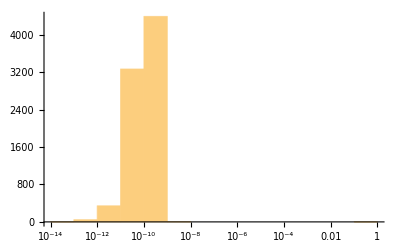

```mathematica
Histogram[Abs[rCorrNoRoot["ExplicitValues"]-Extract[mcPCC,rCorrNoRoot["ExplicitPositions"]]],"Log"]
```

```mathematica
Max[Abs[rCorrNoRoot["ExplicitValues"]-Extract[mcPCC,rCorrNoRoot["ExplicitPositions"]]]]
```

```mathematica
Extract[mcPCC,rCorrNoRoot["ExplicitPositions"]]
```

```mathematica
rCorrNoRoot["ExplicitValues"]==Extract[mcPCC,rCorrNoRoot["ExplicitPositions"]]
```

False

```mathematica
Complement[rCorrNoRoot["ExplicitValues"],Extract[mcPCC,rCorrNoRoot["ExplicitPositions"]]]
```

```mathematica
Length[Intersection[rCorrNoRoot["ExplicitPositions"],mcPCC["ExplicitPositions"]]]
```

8052

```mathematica
diffpos=Complement[mcPCC["ExplicitPositions"],rCorrPs["ExplicitPositions"]];
```

```mathematica
Length[diffpos]
```

1946

```mathematica
missingPs=Extract[mCorrPs, diffpos];
```

```mathematica
Max[10^-missingPs]
```

0.0000991377

```mathematica
Min[10^-missingPs]
```

0.0000379407